Zero temperature, weak coupling  mean 
fmQ1 = (0.79773-24.8496 x+118.431 x^2)/(74.4694+4.64388 x+87.1177 x^2)
Zero temperature, weak coupling varience 
fvQ1=(-36.9967+2092.39 x^2+192.179 x^4)/(137.527+213.194 x^2+37.4426 x^4)
Zero temperature, strong coupling  mean
fmQ2 =(-0.721052-37.7942 x+366.519 x^2)/(75.0737-20.7923 x+56.3204 x^2)
Zero temperature, strong coupling varience
fvQ2 =(-0.0622622+5.20661 x^2+2.38683 x^4)/(0.0884535+0.0753477 x^2+0.081465 x^4)

```mathematica
mQ1 = {1.8405812081189988*^-10,0.000125006,0.0149407,0.0527793,0.109437,0.179565,0.257561,0.338403,0.418743,0.494158,0.565278,0.630474,0.689323,0.742772,0.790284,0.833404,0.871637,0.906254,0.936514,0.96345,0.987059,1.00899,1.02938,1.04507,1.06078,1.07599,1.08887,1.10101,1.11659,1.12763,1.13799,1.14702,1.15325,1.16093,1.16842,1.1755,1.18244,1.1888,1.19463,1.2005,1.2055,1.21023,1.21496,1.21905,1.22305,1.22636,1.23099,1.23482,1.23823,1.24121,1.24442,1.2473,1.25,1.25295,1.25575,1.25865,1.26069,1.26272,1.26491,1.26667,1.26852,1.27104,1.27263,1.27493,1.27715,1.27928,1.28192,1.28402,1.28552,1.28697,1.28791,1.28945,1.28997,1.29136,1.29285,1.2942,1.29615,1.29773,1.29923,1.29983,1.30039,1.30147,1.30207,1.30252,1.30365,1.30469,1.30589,1.30695,1.30764,1.30789,1.30862};
```

```mathematica
vQ1 ={2.388012295509135*^-21,1.0962176467827036*^-11,0.22226779899688334,0.7689605765289165,1.5454429711213857,2.4349901301247976,3.3319835566934977,4.159413573907889,4.878809642762786,5.463425059656779,5.930415546689885,6.287881389885476,6.550029402798663,6.739656089478035,6.8686396964418845,6.969533766236356,7.034298189167698,7.0825144237258675,7.09218382905461,7.107908192951239,7.105868935206357,7.1040143452194755,7.135353043395648,7.0958232780138495,7.019626204758704,6.964164746444448,6.877792717994686,6.80450657837212,6.802713572645995,6.751421973677694,6.719567498215516,6.679209152180881,6.587909046854928,6.506494511139,6.483101691454682,6.4547773379681255,6.47504271718884,6.435296267847235,6.4241818779686835,6.436691209170958,6.390489825248273,6.347171247780086,6.326882620857347,6.285476862927391,6.241912729027859,6.146558808186752,6.143313703362571,6.170596285023927,6.127426710800677,6.0436976570521965,6.043863114724729,6.009283215747681,5.934907555377326,5.922303044312204,5.920435533518504,5.889835821992295,5.879871915580752,5.845003389549144,5.794948833388687,5.748704694598329,5.711934365562274,5.736820815391525,5.701328315461925,5.683114886874477,5.704713150730175,5.695003581332782,5.7589521348342965,5.768445794478453,5.7391347482131,5.678812468470714,5.640809180104151,5.591644585199991,5.494971983829895,5.516715800048563,5.580703578049837,5.521597318487775,5.546808868560515,5.519079580818103,5.542721025654048,5.505447092813535,5.4630750193018205,5.465350791474617,5.462030042284525,5.374639359145459,5.426424785690702,5.363041251517956,5.360086108833599,5.409943385206222,5.428667762923505,5.343840212704828,5.357210259661553};
```

```mathematica
times = Range[0,9,.1];
```

```mathematica
mQ11 = Transpose[{times,mQ1}];
vQ11 = Transpose[{times,vQ1}];
```

```mathematica
(*fmQ1 =(1.7765607620411137-55.340577030333385 x+263.749002382029 x^2)/(165.8450000129009+10.342024404747429 x+194.01299910742677 x^2)(* (1.2141351006018166 x^2)/(1.263506999696822+0.9201674520774232 x^2)*);*)
```

```mathematica
NonlinearModelFit[mQ11,((a*x^4)+b*x^2+ c)/( h + m * x^4 + (l*x^2) ),{m,l,a,b,c,h},x]
```

FittedModel[…]

```mathematica
%204["BestFit"]
```

```mathematica
fmQ1=(-18.14788800334711+727.6164746500937 x^2+3.6984014025262195 x^4)/(696.0326879329675+566.0925233473968 x^2+2.5729833613717155 x^4)
```

(-18.1479+727.616 x^2+3.6984 x^4)/(696.033+566.093 x^2+2.57298 x^4)

```mathematica
%8["BestFit"]
```

(0.79773-24.8496 x+118.431 x^2)/(74.4694+4.64388 x+87.1177 x^2)

```mathematica
%273["BestFit"]
```

```mathematica
fmQ1 = (0.7977298143828709-24.849601967795028 x+118.43132237700311 x^2)/(74.46944812867243+4.643883433929749 x+87.11773631258589 x^2)
```

(0.79773-24.8496 x+118.431 x^2)/(74.4694+4.64388 x+87.1177 x^2)

```mathematica
fmQ1=NonlinearModelFit[mQ11,a-a/(1 + b*x + d*x^2+f*x^3+g*x^4),{a,b,c,d, f, g,h},x]["BestFit"]
```

1.3343-1.3343/(1-0.174194 x+1.05718 x^2-0.158078 x^3+0.0128602 x^4)

```mathematica
fmQ1=NonlinearModelFit[mQ11,(a*x^2+b*x)/(f*x^2+ g *x+h),{p,q,a,b,c,g,f,h,d,k},x]["BestFit"]
```

(-97.817 x+536.548 x^2)/(351.553+26.2609 x+395.255 x^2)

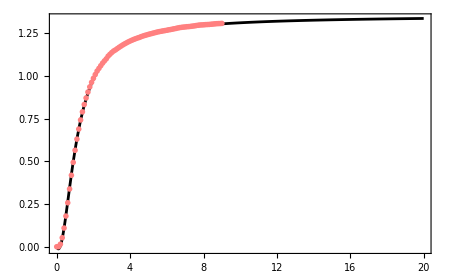

```mathematica
Show[{Plot[fmQ1,{x,0,20}, PlotStyle->{Black}, PlotRange->All], ListPlot[mQ11, PlotStyle->{Pink},PlotRange->All,PlotMarkers->"OpenMarkers"]}, Frame->True]
```

```mathematica
(*Chop[Integrate[0.5*x*Exp[-x/5]*(1- Cos[x *t]),{x,0,1000}]]*)
```

```mathematica
fvQ1=NonlinearModelFit[vQ11,(p*x+a*x^2+ c)/(q*x+f*x^2 + h),{p,q,a,b,c,g,f,h,d,k},x]["BestFit"]
```

(-14.6645+116.278 x+204.324 x^2)/(46.9352-38.5254 x+43.725 x^2)

```mathematica
%197["BestFit"]
```

```mathematica
fvQ1=(-14.66454601165065+116.27827387615383 x+204.323985656153 x^2)/(46.9351510493286-38.52543684493683 x+43.72499793001136 x^2)
```

(-14.6645+116.278 x+204.324 x^2)/(46.9352-38.5254 x+43.725 x^2)

```mathematica
%12["AdjustedRSquared"]
```

0.999793

```mathematica
%12["BestFit"]
```

```mathematica
fvQ1=(-36.996738586254835+2092.3857974605553 x^2+192.17874765182972 x^4)/(137.52732786600183+213.1941345843638 x^2+37.442554892992945 x^4)
```

(-36.9967+2092.39 x^2+192.179 x^4)/(137.527+213.194 x^2+37.4426 x^4)

```mathematica
%290["BestFit"]
```

```mathematica
fvQ1 = (0.034753970070870284-5.990008169498663 x+47.30971567400761 x^2+0.40426297891232765 x^3+5.43830698141061 x^4)/(0.6221237095878007-0.15376732850690808 x+0.617925416321833 x^2+0.29893945223962287 x^3+0.15523236176837013 x^4)
```

(0.034754-5.99001 x+47.3097 x^2+0.404263 x^3+5.43831 x^4)/(0.622124-0.153767 x+0.617925 x^2+0.298939 x^3+0.155232 x^4)

```mathematica
fvQ1=NonlinearModelFit[vQ11,a-(a+c*x +b*x^2)/(1+ d*x +f*x^2+g*x^3+h*x^4),{a,b,c,d, f,g,h},x]["BestFit"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

4.59328-(4.59328+966.99 x-1259.32 x^2)/(1+184.861 x-128.955 x^2+169.903 x^3+0.0352388 x^4)

```mathematica
fvQ1=NonlinearModelFit[vQ11,(a*x^4+c*x^2)/(f*x^4+h*x^2 +k),{a,b,c,f,g,h,d,k,j},x]["BestFit"]
```

(1478.77 x^2+150.5 x^4)/(108.058+145.549 x^2+29.1615 x^4)

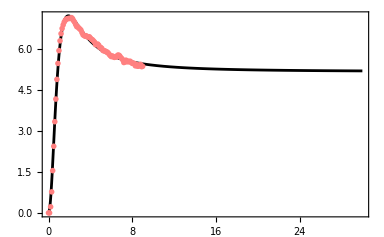

```mathematica
Show[{Plot[fvQ1,{x,0,30}, PlotStyle->{Black}, PlotRange->All], ListPlot[vQ11, PlotStyle->{Pink},PlotRange->All,PlotMarkers->"OpenMarkers"]}, Frame->True]
```

```mathematica
mQ2={3.567500254549793*^-10,0.0006249022715874813,0.07475743944316672,0.26482406719502755,0.5521799503863928,0.9119290857274037,1.3168504998238864,1.7422771450006447,2.17107905034659,2.5819995675126126,2.973477572822831,3.336500188445349,3.6682378306054875,3.9697593161605367,4.241974987188256,4.486313857401634,4.7040500542418195,4.899145135225017,5.0730658507889945,5.226317732080106,5.364379841974493,5.4875919731559115,5.597623523602879,5.6946640948493865,5.782126723837142,5.857089773783587,5.926123146076309,5.988000238266635,6.042783611751876,6.093582291480446,6.1370235398242325,6.176912152885097,6.2127126842769025,6.246164732868617,6.275766185118161,6.301046836162108,6.324806458942082,6.3460786142491274,6.365894095387877,6.383262851581314,6.399092724889714,6.412904350419165,6.425392819925894,6.437065585311147,6.447319023271443,6.458506926281032,6.467857001161147,6.476448462152278,6.483314234948074,6.490561225892032,6.49610631233362,6.5025787152595065};
```

```mathematica
vQ2={2.195244462453438*^-20,0.009371395753627922,1.1181207834869096,3.9159771787177884,7.779134597952304,12.533408214852233,17.16137414676287,21.449586559175412,24.974156435229986,28.06993039742016,30.683596546347133,32.41980056410942,33.7234034192811,34.680247208055526,35.16160082367111,35.09742742486684,35.648746738826546,35.57440497811088,35.350140859729066,34.80430349625048,35.0278773360662,34.66033482177102,34.07603551851091,34.112337445649835,33.84805433164526,33.52848221419654,33.560742958917636,33.33405025135368,33.01494332854216,33.03562798468398,32.77981731888517,32.44741065983405,32.36345089773603,32.18069818435158,31.86337119612135,31.829994997465533,31.64489548286293,31.47468935693999,31.38027257734806,31.205824724472315,31.20213539470336,31.219872174909554,31.10880889853901,31.02153237674974,30.949573073941387,30.90297019608846,30.875796581577276,30.884220382065564,30.85015172556796,30.850167425902278,30.77990920174844,30.763159456872636};
```

```mathematica
times = Range[0,(Dimensions[mQ2][[1]]-1)*0.1,.1];
mQ21 = Transpose[{times,mQ2}];
vQ21 = Transpose[{times,vQ2}];
NonlinearModelFit[mQ11,((a*x^2)+b*x +c)/(f*x^2 + g *x + h),{d,a,b,c,g,f,h},x]
```

FittedModel[…]

```mathematica
fmQ2=NonlinearModelFit[mQ21,(a*x^2+b*x)/(f*x^2 +g*x+ h),{p,q,a,b,c,g,f,h,d,k},x]["BestFit"]
```

(-3.37036 x+30.2561 x^2)/(6.13764-1.71698 x+4.64394 x^2)

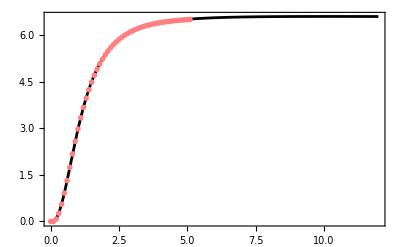

```mathematica
Show[{Plot[fmQ2,{x,0,12}, PlotStyle->{Black}, PlotRange->All], ListPlot[mQ21, PlotStyle->{Pink},PlotRange->All,PlotMarkers->"OpenMarkers"]}, Frame->True]
```

```mathematica
NonlinearModelFit[vQ21,(p*x^4+a*x^2+ c)/(q*x^4+f*x^2 + h),{p,q,a,b,c,g,f,h,d,k},x]
```

FittedModel[…]

```mathematica
%25["BestFit"]
```

(-0.0622622+5.20661 x^2+2.38683 x^4)/(0.0884535+0.0753477 x^2+0.081465 x^4)

```mathematica
fvQ2 =(-0.0622621557690232+5.206613213470804 x^2+2.3868299537003472 x^4)/(0.08845345985819524+0.07534767526210409 x^2+0.08146503637305612 x^4);
```

```mathematica
NonlinearModelFit[vQ21,1-(1+p*x + q*x^2)/(1+c*x + d*x^2 + f*x^3 + g*x^4),{a,b,c,d, f, g,h, p, q},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[…]

```mathematica
FindFit
```

```mathematica
%243["BestFit"]
```

```mathematica
fvQ2=28.154-(690.0882340154283-2209.127885421417 x+1610.1934842832554 x^2)/(24.182511598166098-76.07854440653385 x+80.2084152434405 x^2-49.13684451581834 x^3-13.08611004286535 x^4)
```

28.154-(690.088-2209.13 x+1610.19 x^2)/(24.1825-76.0785 x+80.2084 x^2-49.1368 x^3-13.0861 x^4)

```mathematica
fvQ2=NonlinearModelFit[vQ21,(p*x^4+a*x^2)/(q*x^4+f*x^2+ h),{p,q,a,b,c,g,f,h,d,k},x]["BestFit"]
```

(10.308 x^2+5.35486 x^4)/(0.191549+0.135901 x^2+0.182081 x^4)

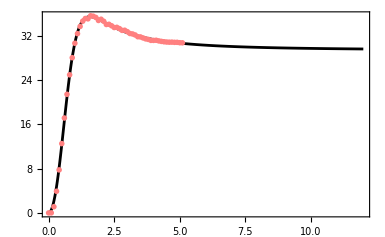

```mathematica
Show[{Plot[fvQ2,{x,0,12}, PlotStyle->{Black}, PlotRange->All], ListPlot[vQ21, PlotStyle->{Pink},PlotRange->All,PlotMarkers->"OpenMarkers"]}, Frame->True]
```

```mathematica
mQ1T={1.28184*10^-9,0.000125016,0.0149407,0.0527793,0.109492,0.179714,0.257827,0.338543,0.418418,0.494688,0.565745,0.630967,0.690042,0.743125,0.790409,0.830671,0.86711,0.900391,0.934133,0.96162,0.98578,1.00857,1.02863,1.0469,1.06386,1.07952,1.09362,1.10563,1.11736,1.12783,1.13792,1.14748,1.15518,1.16357,1.17205,1.17849,1.185,1.19102,1.19663,1.20238,1.20774,1.21311,1.21831,1.22336,1.22783,1.23232,1.23596,1.23959,1.24307,1.24626,1.24941,1.25261,1.25537,1.25756,1.26185,1.2641,1.267,1.26976,1.27134,1.27358,1.2757,1.27811,1.28014,1.28253,1.28432,1.28651,1.28843,1.28987,1.29194,1.29386,1.29512,1.29662,1.29797,1.29947,1.30075,1.30158,1.30269,1.30437};
vQ1T={1.52765*10^-19,1.29853*10^-11,0.222268,0.768962,1.54627,2.43703,3.33598,4.16144,4.87805,5.46658,5.93303,6.29802,6.56009,6.75917,6.88122,6.9579,7.00834,7.05203,7.09676,7.1074,7.09422,7.09492,7.06976,7.05943,7.02659,7.01174,6.98874,6.94975,6.92666,6.87033,6.82604,6.81866,6.77103,6.78946,6.7689,6.74453,6.69865,6.68895,6.6491,6.63382,6.61681,6.59828,6.5883,6.57448,6.53702,6.51335,6.50123,6.47266,6.45242,6.43663,6.41145,6.40398,6.39696,6.3583,6.39883,6.37844,6.37246,6.36783,6.33535,6.31856,6.3011,6.28842,6.28327,6.27499,6.23391,6.23538,6.24279,6.22433,6.22512,6.23834,6.22335,6.20217,6.18407,6.16613,6.15115,6.15792,6.15954,6.12447};
mQ2T={5.989396505547515*^-11,0.000156293,0.068149,0.251915,0.531448,0.879885,1.26905,1.67239,2.07241,2.45484,2.81099,3.1358,3.42983,3.6937,3.9292,4.14783,4.33698,4.50524,4.65213,4.78491,4.90307,5.00829,5.10296,5.18729,5.26298,5.33019,5.39062,5.44539,5.49477,5.53949,5.58114,5.61845,5.65127,5.68265,5.71066,5.73606,5.75915,5.78088,5.79952,5.81792,5.83504,5.851,5.86437,5.87663,5.8905,5.90024,5.91109,5.92115,5.9315,5.94033,5.94802,5.95489,5.96197,5.96853,5.97447};
vQ2T= {-1.2140048038597416*^-20,
1.7160845334233402*^-11,1.01466,3.67705,7.51977,11.9595,16.4758,20.629,24.2385,27.2073,29.5224,31.3043,32.6489,33.5964,34.1698,34.6937,34.9072,35.0512,35.1025,35.1262,35.1026,35.0313,34.9231,34.7097,34.5144,34.259,34.0612,33.7719,33.5762,33.4859,33.3815,33.1884,32.9695,32.9359,32.8521,32.6206,32.4722,32.4426,32.1029,32.0842,32.0405,31.9268,31.8834,31.8758,31.8769,31.5497,31.5798,31.4955,31.5215,31.4284,31.346,31.2363,31.1344,31.0485,30.9407};
```

```mathematica
times1 = Range[0,(Dimensions[mQ1T][[1]]-1)*0.1,.1];
times = Range[0,(Dimensions[mQ2T][[1]]-1)*0.1,.1];
mQ1T1 = Transpose[{times1,mQ1T}];
vQ1T1 = Transpose[{times1,vQ1T}];
mQ2T1 = Transpose[{times,mQ2T}];
vQ2T1 = Transpose[{times,vQ2T}];
```

```mathematica
NonlinearModelFit[mQ1T1,((a*x^2)+c)/(f*x^2 + h),{d,a,b,c,g,f,h},x]
```

FittedModel[…]

```mathematica
%107["BestFit"]
```

(-0.362405+19.4267 x^2)/(19.6196+14.7116 x^2)

```mathematica
fmQ1T1 = (-0.3624051600257193+19.42672134356845 x^2)/(19.61962342501185+14.711573091328908 x^2);
```

```mathematica
fmQ1T1=NonlinearModelFit[mQ1T1,(a*x^2 +b*x)/(f*x^2 +g*x+ h),{a,b,g,f,h,d,k},x]["BestFit"]
```

(-0.36018 x+2.01181 x^2)/(1.32323+0.119858 x+1.47309 x^2)

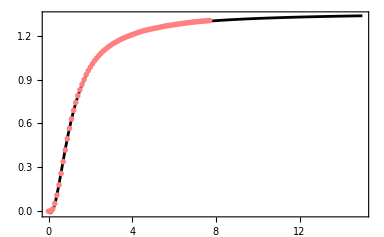

```mathematica
Show[{Plot[fmQ1T1,{x,0,15}, PlotStyle->{Black}, PlotRange->All], ListPlot[mQ1T1, PlotStyle->{Pink},PlotRange->All,PlotMarkers->"OpenMarkers"]}, Frame->True]
```

```mathematica
fvQ1T1=NonlinearModelFit[vQ1T1,(a*x^4+b*x^2)/(f*x^4+g*x^2 + h),{p,q,a,b,c,g,f,h,d,k},x]["BestFit"]
```

(1420.72 x^2+401.678 x^4)/(115.792+129.448 x^2+66.2136 x^4)

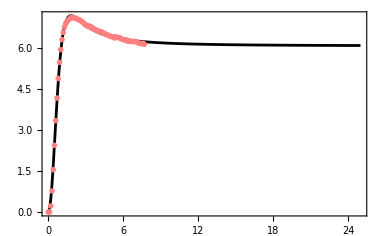

```mathematica
Show[{Plot[fvQ1T1,{x,0,25}, PlotStyle->{Black}, PlotRange->All], ListPlot[vQ1T1, PlotStyle->{Pink},PlotRange->All,PlotMarkers->"OpenMarkers"]}, Frame->True]
```

```mathematica
NonlinearModelFit[mQ2T1,(b*x +(a*x^2)+c)/(g*x+(f*x^2 + h)),{d,a,b,c,g,f,h},x]
```

FittedModel[…]

```mathematica
fmQ2T1=NonlinearModelFit[mQ2T1,(a*x^2+b*x)/(f*x^2 +g*x+ h),{a,b,g,f,h},x]["BestFit"]
```

(-31.2982 x+228.368 x^2)/(42.171-9.42199 x+37.5266 x^2)

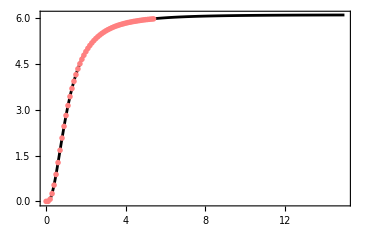

```mathematica
Show[{Plot[fmQ2T1,{x,0,15}, PlotStyle->{Black}, PlotRange->All], ListPlot[mQ2T1, PlotStyle->{Pink},PlotRange->All,PlotMarkers->"OpenMarkers"]}, Frame->True]
```

```mathematica
NonlinearModelFit[vQ2T1,(p*x+a*x^2+ c)/(q*x+f*x^2 + h),{p,q,a,b,c,g,f,h,d,k},x]
```

FittedModel[…]

```mathematica
fvQ2T1=NonlinearModelFit[vQ2T1,(a*x^4+b*x^2)/(f*x^4+g*x^2 + h),{p,q,a,b,c,g,f,h,d,k},x]["BestFit"]
```

(22.1913 x^2+9.46 x^4)/(0.403431+0.356355 x^2+0.314482 x^4)

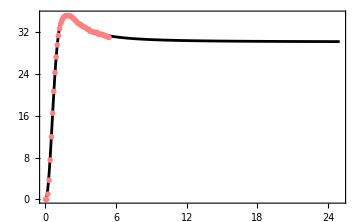

```mathematica
Show[{Plot[fvQ2T1,{x,0,25}, PlotStyle->{Black}, PlotRange->All], ListPlot[vQ2T1, PlotStyle->{Pink},PlotRange->All,PlotMarkers->"OpenMarkers"]}, Frame->True]
```

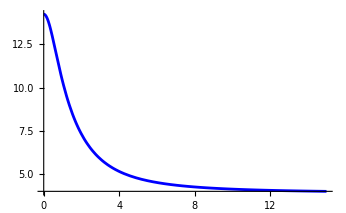

```mathematica
Plot[fvQ1/fmQ1,{x,0,15}, PlotStyle->{Blue}, PlotRange->All]
```

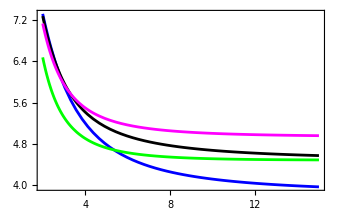

```mathematica
Show[Plot[fvQ1/fmQ1,{x,2,15}, PlotStyle->{Blue}, PlotRange->All],Plot[fvQ2/fmQ2,{x,2,15}, PlotStyle->{Green}, PlotRange->All],Plot[fvQ1T1/fmQ1T1,{x,2,15}, PlotStyle->{Black}, PlotRange->All],Plot[fvQ2T1/fmQ2T1,{x,2,15}, PlotStyle->{Magenta}, PlotRange->All],Frame -> True ]
```

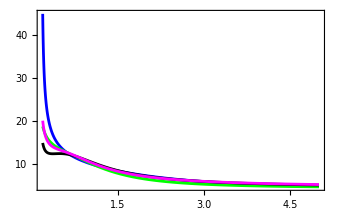

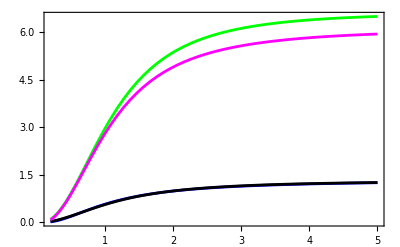

```mathematica
Show[Plot[fmQ1,{x,0.2,5}, PlotStyle->{Blue}, PlotRange->All],Plot[fmQ2,{x,0.2,5}, PlotStyle->{Green}, PlotRange->All],Plot[fmQ1T1,{x,0.2,5}, PlotStyle->{Black}, PlotRange->All],Plot[fmQ2T1,{x,0.2,5}, PlotStyle->{Magenta}, PlotRange->All],Frame -> True ]
```

FANO MATTER in independent-boson model

```mathematica
Qvar[β_,ω_,t_, α_]:= α *ω* Exp[-ω/5]* Coth[(β*ω)/2]*(1 - Cos[ω*t])
Qmean [β_,ω_,t_, α_]:=  α * Exp[-ω/5]*(1 - Cos[ω*t])
```

```mathematica
Plot[List[NIntegrate[Qvar[1,ω,t,1.5],{ω,0,100}],{t,0.00001,10,0.1}],{t,0.00001,10,0.1}]
```

Plot::pllim: Range specification {t,0.00001,10,0.1} is not of the form {x, xmin, xmax}.

Plot[{NIntegrate[Qvar[1,ω,t,1.5],{ω,0,100}],{t,0.00001,10,0.1}},{t,0.00001,10,0.1}]

```mathematica
Array[NIntegrate[Qvar[1,ω,t,1.5],{ω,0,100}],{t,0.00001,10,0.1}]
```

NIntegrate::inumr: The integrand 1.5 ⅇ^(-ω/5) ω (1-Cos[t ω]) Coth[ω/2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[NIntegrate[Qvar[1,ω,t,1.5],{ω,0,100}],{t,0.00001,10,0.1}].

```mathematica
Varval = {};
Do[ 
	val = Array[NIntegrate[Qvar[1,ω,t,1.5],{ω,0,100}];
Append[val,Varval];
,{t,0.00001,10,0.01}]
```

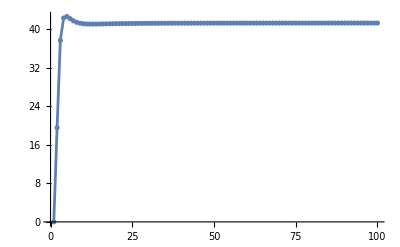

```mathematica
ListPlot[{0,19.550809586695387,37.687679378599455,42.337506846924455,42.663966552683874,42.201874075054896,41.75534648974618,41.44766233031043,41.259925825986286,41.15484302859491,41.10206227529248,41.080752145214056,41.077569177733,41.08428675516181,41.095974817759426,41.10976094322042,41.12402155748611,41.1378835963498,41.15091199164513,41.162923074829635,41.173875132016825,41.1837989295458,41.19276372764472,41.200852618934334,41.208151798448355,41.21474523322147,41.22070913995331,41.22611405026679,41.23102179562864,41.235487470263685,41.239560067183234,41.243281582127246,41.246690191781774,41.24981831016358,41.25269501391117,41.25534598412251,41.25779315602539,41.260056959602075,41.26215441096952,41.26410132854191,41.26591158246868,41.267597132272236,41.269169466124396,41.27063789234164,41.272011552295304,41.2732982616375,41.27450492825356,41.275638355879806,41.27670385863193,41.27770705407815,41.2786524991375,41.27954443155657,41.280387053610355,41.28118352300008,41.2819374884888,41.28265166543508,41.28332881765256,41.28397161548142,41.28458201375638,41.285162494021044,41.28571468923467,41.286240515081126,41.286741690250594,41.2872194846981,41.28767564465034,41.28811115031288,41.28852740769077,41.28892551691008,41.2893063552194,41.28967117637195,41.29002056358131,41.290355600146505,41.29067697083481,41.290985328450844,41.291281577274226,41.291566062488734,41.29183964925451,41.29210273784658,41.2923558547274,41.292599643260544,41.29283431263772,41.29306056824331,41.29327861550595,41.29348891032404,41.293691893849484,41.29388770590284,41.29407692448875,41.294259624730216,41.29443622180298,41.294606996098764,41.29477206333155,41.29493189023691,41.29508647059717,41.295236192068984,41.29538120923304,41.29552163711523,41.29565784470482,41.29578978062293,41.29591780921106,41.296041984904974},Mesh->All,Joined->True, PlotRange->All]
```